Initial Graph:

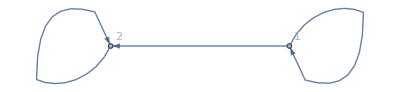

Frequency Vector: {{{1,γ/(1-γ)},{1/(1-γ),0}},{{0,1/(1-γ)}}}

#############################################################################################

Equation List: {r[1]+(γ r[2])/(1-γ),r[1]/(1-γ)}

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 1

Inequalities used: r[2]>r[1]

Integration: γ/(3-3 γ)

Measure: 1/2

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 2

Inequalities used: r[2]<r[1]

Integration: γ/(3-3 γ)

Measure: 1/2

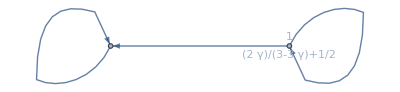

1/2+(γ (-8+3 γ-2 γ^2+γ^3))/(12 (-1+γ))

```mathematica
(*Be sure to run "runThisFileFirst.nb"*)
(*To Run, press Shift+Enter. Or, at top, Evaluation -> Evaluate Cells*)
(*Note: If running forever,(usually #states > 7), then Evaluation -> Quit Kernal -> local*)
vertexAndNodes = {1->2,1->3, 2->3, 3->4, 4->4};
vertexAndNodes = {1->2,1->3, 2->3, 3->4, 4->4};
vertexAndNodes = {1->2,1->4, 2->3, 2->1, 2->3, 2->6, 3->1, 3->2, 3->5, 4->1, 4->5, 4->6, 5->3, 5->6, 5->4, 6->2, 6->4, 6->5};
vertexAndNodes = {1->5, 5->6, 6->1, 1->2, 2->3, 3->4, 4->2, 2->2}; (*This one breaks it*)
vertexAndNodes = {1->1, 1->2, 2->2}; 
(*            graph    , First/All, None/Basic/Measure*)
powerOfGraph[vertexAndNodes, "First", "Basic"]
(*
First - calculate Power for first state only;
All - Calcuate Power for all states;
None - Display only final power graph;
Basic - Display basic info such as frequency vector, inequalities, and integrations.;
Measure - Display Measure and power graph. Only works with "First";
*)

(*If you'd like to compare a handwritten equation with the calculated power:*)
eq = 2/3*γ + 5/12*γ^2 + 7/12*γ^3 + 1/2 *γ^4/(1-γ);
powerCheck[eq]
(*Note: use the ";" at the end to suppress output*)
```